# Physics 230 -- Lab 12 (Integral Transforms)

## Branton J. Campbell, BYU Physics & Astronomy, Winter 2010 R. Steven Turley, BYU Physics & Astronomy, Fall 2011

The purpose of an integral transform is to transform a function from one basis to another where it can be more easily understood.  These transforms are probably most easily understood by starting with transforms using a finite set of basis functions (series transforms) and then generalizing these to an infinite basis (integral transforms).

## Introduction (15 min)

### Finite Bases (5 min)

There are many examples in physics where solutions to problems are expressable as a linear sum of functions.  For instance, the waves produced in a musical instrument are often quite complex.  However, when seen as a sum of the various allowed harmonics, they are much easier to understand.  As an example,

For example, consider the motion of a vibrating string which is clamped on both ends.  If the string has a tension T and a mass per unit length λ, then the speed of of wave pulse travelling along wtih string is v=√(T/λ).   Any allowed vibration of the string can be expressed as a sum of sine waves whose wavelength makes it zero at both ends of the string.  In other words, if the string has  length L, the allowed wavelengths are λ=(2L)/n, where n is a positive integer.  The frequency of each sine wave is given by f=v/λ. Consider the complicated motion with random amplitudes of the first ten allowed frequencies in a string of length 1 and speed 1.

```mathematica
funcs[x_,t_]=Table[RandomReal[] Sin[x n Pi] Sin[Pi n t],{n,1,5}]
Animate[Plot[Total[funcs[x,t]],{x,0,2},PlotRange->{All, {-3,3}}],{t,0,10}]
```

{0.805099 Sin[π t] Sin[π x],0.324566 Sin[2 π t] Sin[2 π x],0.519933 Sin[3 π t] Sin[3 π x],0.245581 Sin[4 π t] Sin[4 π x],0.602146 Sin[5 π t] Sin[5 π x]}

On the other hand, each of the individual contributing waves is a simple sine function.

```mathematica
Animate[Plot[funcs[x,t][[2]],{x,0,2},PlotRange->{All, {-3,3}}],{t,0,10}]
```

Another example you have seen of finite bases functions are using polynomials to approximate complicated functions.  For instance the sine integral Si(z)=∫_0^z sin(t)/t dt doesn’t have a nice closed-form expression.  Here is what it looks like near 0.

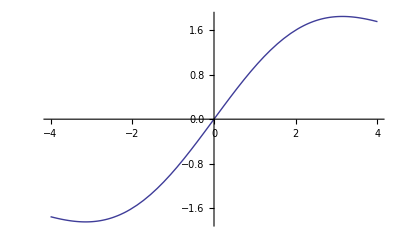

```mathematica
Plot[SinIntegral[z],{z,-4,4}]
```

A series expansion of this function is an approximate expression using powers of z as basis functions.

z^9/3265920-z^7/35280+z^5/600-z^3/18+z

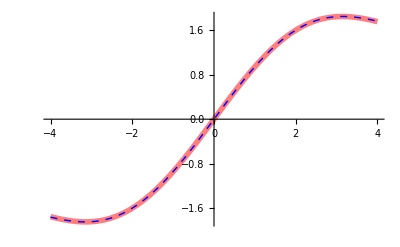

```mathematica
si[z_]:=Evaluate[Series[SinIntegral[z],{z,0,10}]//Normal]
si[z]
Plot[{SinIntegral[z],si[z]},{z,-4,4},PlotStyle->{{Red,Thickness[0.01],Opacity[0.5]},{Blue,Dashed}}]
```

### (#1) Infinite Bases (5 min)

Some functions require an infinite number of basis functions for their exansion.  In those cases, the sums above are replaced with integrals.  These will be the principal focus of this lab.  These integral transforms change how a function is expressed from one kind of representation to another.  This functions can either be real-valued functions of complex functions.

Integral transforms then are essentially treating a function like a vector and transforming it into a new coordinate system.  Physicists are especially fond of Fourier transforms, which transform time-dependent functions into frequency-dependent functions.  In other words, they take a quantity that has been expressed in the time coordinate system and transform it into the frequency coordinate system.  While the frequency domain is certainly more abstract than the time domain, the structure and the dynamics of a complicated physical system are often more clear there.  In this lab, you will learn how to use Mathematica to perform Laplace and Fourier transforms to continuous functions and discrete datasets.

Another example of using a Fourier Transform to is in quantum mechanics to move back and forth between a representation expression in terms of a particle’s position probability and a representation based on its momentum probability.  The square of the magnitude of the wave function of a particle ψ(x) gives the probability of finding the particle at position x.  On the other hand, the state of the particle can also be represented by the Fourier Transform of ψ, ϕ(k).  The square of this function represents the probability of the particle having a momentum p=ℏk.  Both the position and momentum representations are complete descriptions of the state of the particle, one is in terms of a momentum basis and the other in terms of a position basis.

Execute the cell below to compare the position and momentum wave functions which have a gaussian (normal) distribution for their shape.  Play with the width of the distributions specified by σ.  What happens to the width of the momentum distribution if you make the width of the spatial distribution smaller?  (This is the basis of the Heisenberg Uncertainty Principle, which you will learn about in Physcis 222 if you haven’t already.)

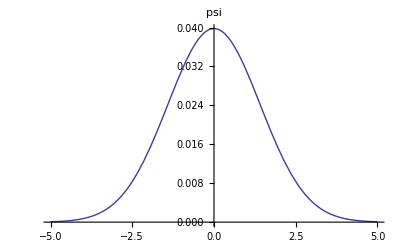

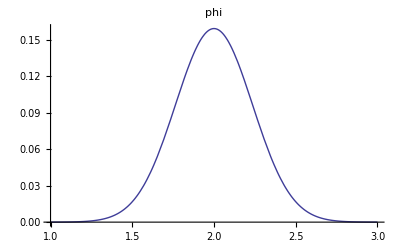

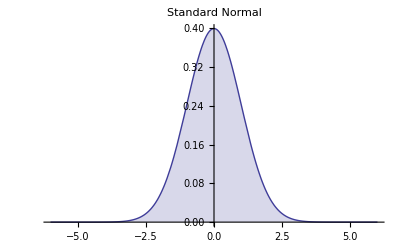

```mathematica
psi[x_,sigma_,k0_]:=1/(Sqrt[2 Pi] sigma) Exp[-x^2/(2 sigma^2)] Exp[-I k0 x]
Plot[Abs[psi[x,2,3]]^2,{x,-5,5},PlotLabel->"psi"]
phi[k_,k0_,sigma_]:=FourierTransform[psi[x,sigma,k0],x,k]
Plot[Abs[phi[k,2,3]]^2,{k,1,3},PlotLabel->"phi"]
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,{1}}],{x,-6,6},Filling->Axis,PlotLabel->"Standard Normal"]
```

Discuss what you learned about these two graphis with your TA.

### Reading (5 min)

Follow the Calculus link in the Mathematics and Algorithms section of the DC home page, and then click the link to the guide page on Integral Transforms.  In this lab, you will gain experience with many of the functions that you see listed there.  After you have completed the lab, you will also find the tutorials on Integral Transforms and Related Operations and Discrete Fourier Transforms to be useful quick references.

## Fourier transforms (30 min)

The Fourier transform (FourierTransform) of a function f(t) is defined as F(ω) = ℱ_[f(t)] = 1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(i ω t)ⅆt.  This remarkable little integral transforms time-dependent function f(t) into frequency spectrum F(ω).  If we were to construct f(t) by superposing a continuous mixture of waves of every possible frequency, F(ω) would tell us how much of each frequency to mix in.  We say that the contribution associated with frequency ω has a complex amplitude F(ω) and a phase factor ⅇ^(i ω t).  To add all of the contributions together, we just integrate over ω as follows:  f(t) =  ℱ^-1[F(ω)] = 1/(√(2π))∫_(-∞)^∞ F(ω)ⅇ^(-i ω t)ⅆω.  This is the inverse Fourier transform (InverseFourierTransform).

The FourierTransform can also be used to transform from distance (x) to wavenumber (k).  In this case, the Fourier Transform is F(k) = ℱ_[f(x)] = 1/(√(2π))∫_(-∞)^∞ f(x)ⅇ^(i k x)ⅆx and the inverse transform is  f(x) =  ℱ^-1[F(k)] = 1/(√(2π))∫_(-∞)^∞ F(k)ⅇ^(-i k x)ⅆk.

### (#2) The Dirac delta and the step function (15 min)

(a) A normalized Gaussian peakshape has the form 1/(√(2π)σ)ⅇ^(-(x-x_0)^2/2 σ^2), where x_0 is the location of the peak center and σ is the peak width.  In the cell below, we define a general Gaussian function for future use.  Evaluate the cell to plot two Gaussians, a narrow peak of width σ = 0.01 centered at x = 0.1 and a broader peak of width σ = 0.1 centered at x = 0.

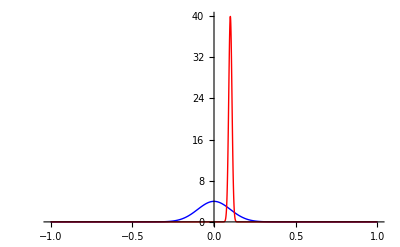

```mathematica
gauss[x_, x0_, sig_] := Exp[-(x-x0)^2/(2 sig^2)]/(Sqrt[2 Pi] sig)
Plot[{gauss[x,0,0.1],gauss[x,0.1,0.01]},{x,-1,1},PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red}}]
```

(b) Notice that the peak height increases when the width decreases, so that the integrated area remains constant.  To describe this effect, we say that the prefactor of 1/(√(2π)σ) "normalizes" the area.  Integrate gauss[x, x0, sig] over the range {x, -Infinity, Infinity} to show that the area under the peak is always equal to 1.  You may need to include Assumptions→{sig > 0} as an option.

```mathematica
Integrate[gauss[x,x0,sig],{x,-∞,∞},Assumptions->{sig>0}]
```

1

(c) In the limit that σ → 0, the Gaussian peakshape becomes the famous Dirac delta (DiracDelta) function, δ(x).  This special function is infinite at the point x = 0, and zero everywhere else.  You will encounter it often in upper-level physics courses as an impulse function (i.e. an infinitely-short pulse).  In the cell below, Integrate the DiracDelta function to show that  ∫_(-∞)^∞ δ(x)ⅆx=1.  Thus, even though the peak now has zero width, it is still normalized to have a finite integrated area.

```mathematica
Integrate[DiracDelta[x],{x,-∞,∞}]
```

1

(d) Another important property of the Dirac delta is that it can extract the value of an arbitrary function, f(t), at a specific point, t = t_0.  Show that ∫_(-∞)^∞ f(t) δ(t-t_0)ⅆt=f(t_0) by performing the integral.  You may need to assume that {t0 ∈ Reals}.

```mathematica
Integrate[D[DiracDelta[t-t0],t]*f[t],{t,-∞,∞},Assumptions->{t0∈ Reals}]
```

-f'[t0]

(e) Use the integral formula in the introductory paragraph at the top of this section to compute the Fourier transform of the DiracDelta function, δ(t).  Explain the result to your TA in terms of the integration-properties of the δ(t).  Then use Mathematica's FourierTransform function to achieve the same result.

1/(√(2π))∫_(-∞)^∞ f(t)ⅇ^(i ω t)ⅆt

```mathematica
1/(√(2π))*Integrate[DiracDelta[t]*Exp[I*ω*t],{t,-∞,∞}]
FourierTransform[DiracDelta[t],t,ω]
```

1/(√(2 π))

1/(√(2 π))

(f) Show that the FourierTransform of a constant (e.g. 1/(√(2π))) is δ(ω).  Explain the result to your TA.  Hint: F(ω) = δ(ω) means that the only wave contributing to the time-signal is the ω = 0 wave.  And a zero-frequency wave is just a time-independent constant.

```mathematica
FourierTransform[1/(√(2π)),t,ω]
```

ω

(g) The step function (HeavisideTheta or UnitStep) is a Piecewise function (i.e. it has distinct definitions in distinct regions) defined as h(t) = Piecewise[{{0, t<0}, {1, t>0}}].  It is related to the Dirac delta in that d/(d t)h(t) = δ(t).  Evaluate the cell below to plot h(t)sinc(t), and observe that h(t) has the effect of turning the other function "on" like a light switch at time t = 0.

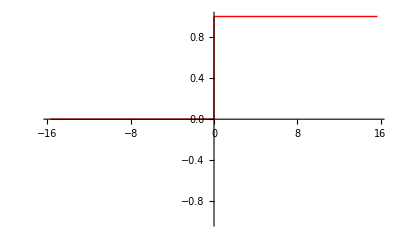
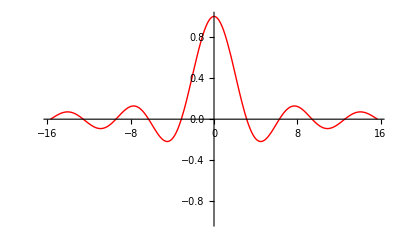
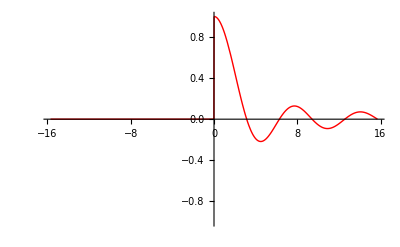

```mathematica
p1 = Plot[UnitStep[t], {t,-5 Pi,5Pi},PlotRange->{-1,1}, ExclusionsStyle->Automatic,PlotStyle->{Thick,Red}];
p2 = Plot[Sinc[t], {t,-5Pi,5Pi},PlotRange->{-1,1}, ExclusionsStyle->Automatic,PlotStyle->{Thick,Red}];
p3 = Plot[UnitStep[t]*Sinc[t], {t,-5Pi,5Pi},PlotRange->{-1,1}, ExclusionsStyle->Automatic,PlotStyle->{Thick,Red}];
{p1,p2,p3}
```

### (#3) Fourier transforms of sinusoidals (10 min)

(a) Evaluate the cell below to compute the FourierTransform of a complex sinusoid of the form f(t) =ⅇ^(i ω_0 t).  Look carefully to see how we plot the frequency spectrum for the special case where ω_0= 1.  Demonstrate to your TA that there is a connection between the exponential form of f(t ), the Dirac deltas in F(ω), and the peaks in the plot.

Note: because the infinitely-sharp Dirac delta is not plottable, it is sometimes helpful to approximate it as sharp Gaussian peak.  We employed a clever pattern-substitution to accomplish this.

ⅇ^(ⅈ t w0)

w+w0

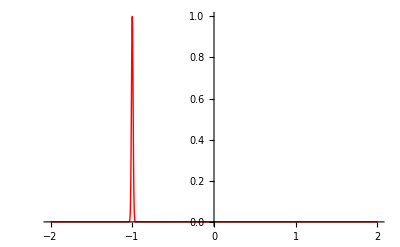

```mathematica
fff = Exp[I w0 t ]//TrigToExp
FFF =FourierTransform[fff,t,w]/Sqrt[2 Pi]//Expand
plotFFF = FFF/.w0->1/.{DiracDelta[x_] -> Exp[-x^2/(2*0.01^2)]};
Plot[plotFFF,{w,-2,2},PlotStyle->{Thick,Red},PlotRange->All]
```

(b) Copy/paste/modify code from the previous cell in order to compute and plot the Fourier transform of f(t) = cos(ω_0 t).  As before, demonstrate to your TA that there is a connection between the exponential form of f(t ), the Dirac deltas in F(ω), and the peaks in the plot.

```mathematica
ffff =Cos[w0*t]//TrigToExp
FFFF =FourierTransform[fff,t,w]/Sqrt[2 Pi]//Expand
plotFFFF = FFFF/.w0->1/.{DiracDelta[x_] -> Exp[-x^2/(2*0.01^2)]};
Plot[plotFFFF,{w,-2,2},PlotStyle->{Thick,Red},PlotRange->All]
```

1/2 ⅇ^(-ⅈ t w0)+1/2 ⅇ^(ⅈ t w0)

w+w0

-Graphics-

### (#4) Fourier transforms of Gaussian peaks (5 min)

(a) The Fourier Transform of a given function rarely looks anything like the original function.  But there is one notable expection to this rule.  Evaluate the cell below to see that the Fourier transform of a Gaussian peak is another Gaussian peak.  In other words, observe that the Fourier transform of  (ⅇ^(-t^2/(2 σ_T^2)))/(√(2π)σ_T) is just (ⅇ^(-ω^2/(2 σ_ω^2)))/(√(2π)σ_ω) to within a proportionality constant, where σ_T is the width of the time-domain peak and σ_ω is the width of the corresponding frequency-domain peak.  We plot both the time-domain (blue) and frequency-domain curves (red) for the special case where σ_T→2.

(ⅇ^(-t^2/(2 σ_T^2)))/(√(2 π) σ_T)

(σ_T ⅇ^(-1/2 w^2 σ_T^2))/(√(2 π))

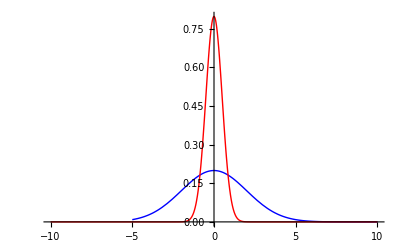

```mathematica
tgauss = Exp[-t^2/2/Subscript[σ, T]^2]/Sqrt[2 Pi]/Subscript[σ, T]
wgauss = FourierTransform[tgauss,t,w,Assumptions->{Subscript[σ, T]>0}]*Subscript[σ, T]
tplot = Plot[tgauss/.Subscript[σ, T]->2,{t,-5,10},PlotRange->All,PlotStyle->{Thick,Blue}];
wplot = Plot[wgauss/.Subscript[σ, T]->2,{w,-10,10},PlotRange->All,PlotStyle->{Thick,Red}];
Show[tplot,wplot]
```

Note that this is the same shape we used in the quantum mechanics part of the introduction.  Notice again the relationships between the width in the time domain and the width in the frequency domain.

In this section I learned that following nterests and developing a unique skill set will be one of the most martketable aspects a person has when searching for a job. The other thing was that being well educated in your field will help you not fall behind in the cutting edge aspects of the field.

## Diffraction optics (40 min)

When light of wavelength λ shines through a 2D mask of lateral dimension a located at z = 0 along the optic axis and then onto a distant screen located at z = L, diffracted light coming from different {x, y} points on the mask will travel different distances in order to reach the same {X, Y} point on the screen, giving rise to phase differences and interference.  We call the resulting interference pattern a "diffraction" pattern.  Under the right conditions, the diffraction pattern on the screen will simply be the Fourier transform of the mask function, or rather its absolute value squared.  (Wow!)

In the following exercises, we will use a Fourier transform to compute some well-known diffraction patterns, though you will notice that we have replaced t with x and ω with k in our equations.  As we mentioned earlier, a spatial frequency (wavevector k) with a position-dependent function just like we can associate a time frequency ω with a function of time.

### (#5) The double slit (10 min)

(a) Evaluate the cell below to create and plot a 1D mask containing two narrow slits separated by a distance d.  This is the famous double-slit problem.  While we will use the ideal mask, we also create an approximate mask function in order to plot it for the special case where d → 2.

2 DiracDelta[d-2 x]+2 DiracDelta[d+2 x]

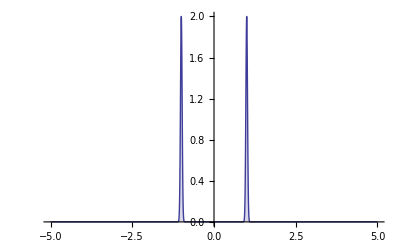

```mathematica
mask=  DiracDelta[x-d/2] + DiracDelta[x+d/2]
maskapprox= mask/.{DiracDelta[x_] -> Exp[-x^2*200]}/.d->2;  (* this is only for plotting purposes *)
Plot[maskapprox,{x,-5,5},PlotRange->All,Filling->Axis]
```

(b) In this cell, compute the Fourier transform of the mask function f(x), use FullSimplify to get a simple expression for F(k), and name the result diffraction.  Then plot F(k) and |F(k)|^2 in separate graphs over the range {k, -16π, +16π} for the special case where d → 2, using {PlotRange → All, Filling → Axis} as options.  Explain the result to your TA, and comment on the similarity of this problem to the earlier problem where you computed the Fourier transform of a cosine function.

```mathematica
Clear["`*"]
```

√(2/π) Cos[(d k)/2]

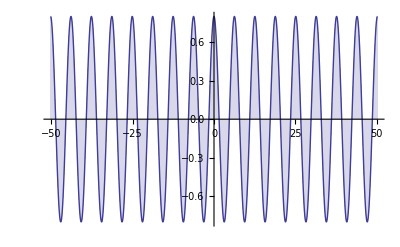

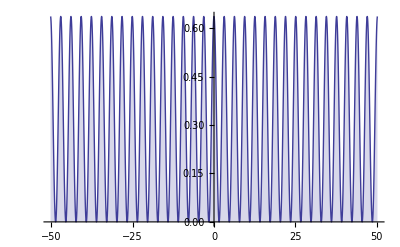

```mathematica
diffraction=FourierTransform[mask,x,k]//FullSimplify
Plot[diffraction/.d->2,{k,-16π,16π},PlotRange->All, Filling->Axis]
Plot[Abs[diffraction/.d->2]^2,{k,-16π,16π},PlotRange->All, Filling->Axis]
```

### (#6) The nonzero-width slit (5 min)

(a) Evaluate the cell below to create and plot a 1D mask containing one uniform aperature of width a.  We plot it for the special case where a → 1/2.

```mathematica
Clear["`*"]
```

Piecewise[{{1, -a/2<x<a/2}, {0, True}}]/a

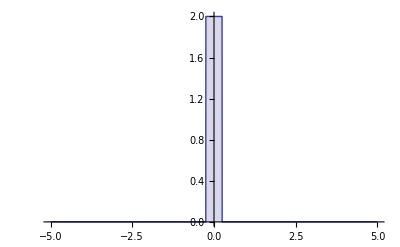

```mathematica
box[x_,c_,a_] := Piecewise[{{1,-a/2<x-c<a/2}},0]/a
mask= box[x,0,a]
Plot[mask/.{a->1/2},{x,-5,5},PlotRange->All,Filling->Axis]
```

(b) In this cell, compute the Fourier transform of the mask function with Assumptions→{a > 0} as an option, use FullSimplify to get a simple expression for F(k), and name the result diffraction.  Then plot F(k) and |F(k)|^2 in separate graphs over the range {k, -16π, +16π} for the special case where a → 1/2, using the same plot options employed above.  You should be able to copy/modify code from the previous exercise.  Do you recognize the Sinc function here?

(√(2/π) Sin[(a k)/2])/(a k)

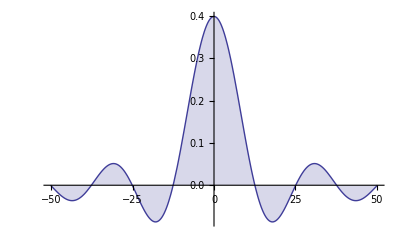

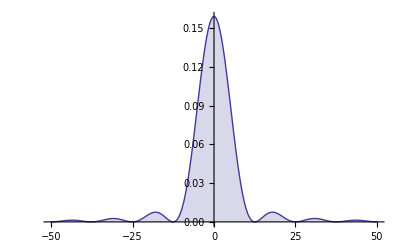

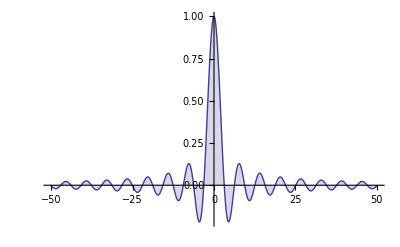

```mathematica
diffraction = FourierTransform[mask,x,k,Assumptions->{a>0}]//FullSimplify
Plot[diffraction/.a->1/2,{k,-16π,16π},PlotRange->All, Filling->Axis]
Plot[Abs[diffraction/.a->1/2]^2,{k,-16π,16π},PlotRange->All, Filling->Axis]
Plot[Sinc[x],{x,-16π,16π},PlotRange->All, Filling->Axis]
```

### (#7) The non-zero-width double slit (5 min)

(a) Evaluate the cell below to create and plot a 1D mask containing two aperatures of non-zero width a separated by a distance d.  We plot it for the special case where d → 4 and a → 1/2.

Piecewise[{{1, -a/2<-d/2+x<a/2}, {0, True}}]/a+Piecewise[{{1, -a/2<d/2+x<a/2}, {0, True}}]/a

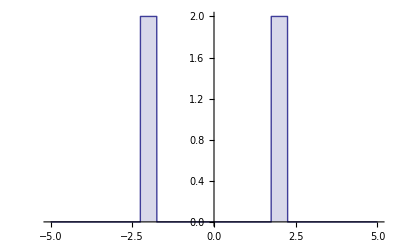

```mathematica
box[x_,c_,a_] := Piecewise[{{1,-a/2<x-c<a/2}},0]/a
mask = box[x,-d/2,a]+box[x,+d/2,a]
Plot[mask/.{d->4,a->1/2},{x,-5,5},PlotRange->All,Filling->Axis]
```

(b) In this cell, compute the Fourier transform of the mask function with Assumptions→{a > 0} as an option, use FullSimplify to get a simple expression for F(k), and name the result diffraction.  Then plot F(k) and |F(k)|^2 in separate graphs over the range {k, -16π, +16π} for the special case where d → 4 and a → 1/2.  You should be able to copy/modify code from the previous exercise.  Comment on the relationship between this diffraction pattern and the previous two (i.e. the double-slit and nonzero-width-slit cases).

(2 √(2/π) Cos[(d k)/2] Sin[(a k)/2])/(a k)

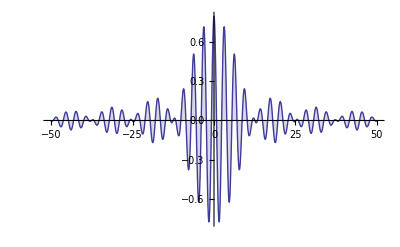

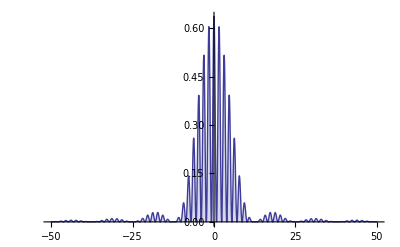

```mathematica
diffraction = FourierTransform[mask,x,k,Assumptions->{a>0}]//FullSimplify
Plot[diffraction/.{a->1/2,d->4},{k,-16π,16π},PlotRange->All, Filling->Axis]
Plot[Abs[diffraction/.{a->1/2,d->4}]^2,{k,-16π,16π},PlotRange->All, Filling->Axis]
```

## Discrete Fourier transforms (25 min)

We won't say much about the discrete Fourier transform here, except that it is used to transform a discrete list of numbers (i.e. data) rather than a continuous function.  The discrete Fourier Transform is what we called a transform series rather than a transform integral in the introduction.

### (#8) Discrete transforms (15 min)

(a)  Evaluate the cell below to define a list of times (called tlist) ranging from 0 to trange in tnum equal steps of tresolution.  This is a discrete set of times at which a function f(t) will be sampled.

```mathematica
trange =20Pi; tnum =128;  omega =1;  (* these can be modified *)
tresolution = trange/(tnum-1)//N;  (* don't change this *)

tlist = Table[t,{t,0,trange,tresolution}];
```

(b) In the next input cell (a few steps down), evaluate Cos[omega*t] at each of the times in tlist above.  Name the result flist and ListPlot it with {PlotRange → All, Joined → True, AxesLabel → {"t", "f(t)"}} as options.

(c) Observe that there is a problem with the time axis -- time was supposed to run from 0 to 20π ≈ 62.8, but appears to run from 1 to 128 (the number of samples) instead.  This is because we haven't included the times in flist.  In the same cell, add another option to your ListPlot that will explicitly define the horizontal time range: DataRange→{0, trange}.

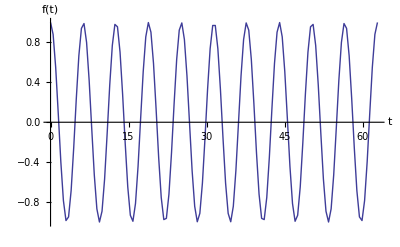

```mathematica
flist =Cos[omega*#]&/@tlist;
ListPlot[flist,PlotRange->All,Joined->True,AxesLabel->{"t","f(t)"},DataRange->{0,trange}]
```

(d) In the next input cell (a few steps down), use Fourier to compute the discrete Fourier transform of flist.  After you observe that the output is complex, go back and employ Re so as to keep only the real parts, suppress the output with a semicolon, and name the result Flist.  Then ListPlot the absolute value of Flist with {PlotRange → All, Joined → True, AxesLabel → {"ω", "F(ω)"}} as options.

(e) Just as before, the horizontal axis appears to be tracking the list position instead of showing the true frequency.  We can certainly use DataRange again; but what maximum frequeny do we use?  Note that when going back and forth between the time and frequency domains, the range in one domain turns out to be the inverse resolution in the other (1/resolution in Hz, or 2π/resolution in radians/second).  In the same cell, add DataRange→{0, 2*Pi/tresolution} as an option to ListPlot.  Your approximate delta function (i.e. sharp peak) should be located at ω = 1 as expected.

(f) What about the second peak out near ω = 12?  Instead of providing the negative side of the frequency spectrum, the discrete transform produces what appears to be a mirror image of the transformed data at the right-hand side of the plot.  We can ignore this by plotting only half of the data.  In the same cell, change your PlotRange to {{0, Pi/tresolution}, All}.  If you haven't noticed already, the effective management of discrete transforms involves a lot of fancy plot options.

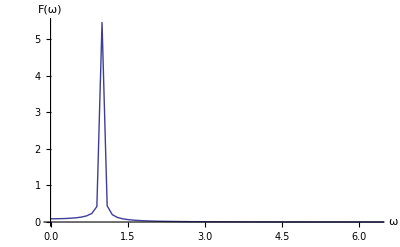

```mathematica
Flist=Re[Fourier[flist]];
ListPlot[Abs[Flist],PlotRange -> {{0,π/tresolution},All}, Joined -> True, AxesLabel -> {"ω", "F(ω)"},DataRange->{0,2π/tresolution}]
```

(g)  In the cell below, use InverseFourier to compute the discrete inverse Fourier transform of Flist, employ Re to obtain the real part, and name the result newflist.  Plot it using the same options that you used with flist earlier.

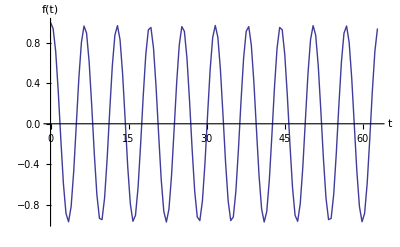

```mathematica
newflist = Re[InverseFourier[Flist]];
ListPlot[newflist,PlotRange->All,Joined->True,AxesLabel->{"t","f(t)"},DataRange->{0,trange}]
```

### (#9) Audio spectra (10 min)

(a) Evaluate the cell below to hear and visualize the C above middle C (523.25 Hz) played on a concert flute.  We have extracted the data from this soundclip in placed it in a list called tdata.  Your TA has headphones available if you want to listen to the clip.

-Graphics-

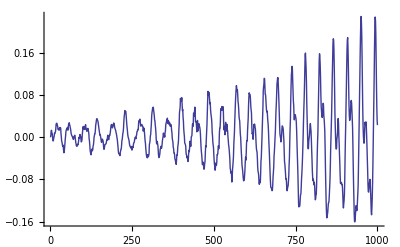

```mathematica
ExampleData[{"Sound","AltoFlute"}]
tdata = %[[1,1,1]];
ListPlot[tdata[[;;1000]],Joined->True]
```

(b) Use Fourier and Re to compute the real part of the discrete Fourier transform of tdata, and ListPlot the result with Joined → True and AxesLabel → {"ν(Hz)", "F(ν)"} as options.  As done in the previous exercise, use the DataRange option to indicate that the frequency spectrum runs from 0 to 22050 Hz, and the PlotRange option to view All of the vertical axis but only the region from 0 to 2500 Hz on the horizontal axis.

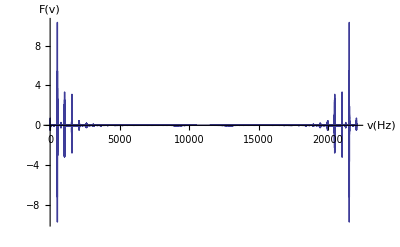

```mathematica
fluteplot=Re[Fourier[tdata]];
ListPlot[fluteplot,Joined->True,AxesLabel->{"v(Hz)","F(v)"},DataRange->{0,22050},PlotRange->{{0,22050},All}]
```

## Fourier Series Expansions (20 min)

We discovered in an earlier exercise that sinuoidal functions yield only discrete delta functions in the frequency domain.  This turns out to be true of any periodic function.  And in the time-domain, any perodic function with period T = (2π)/ω_0 can be written as a discrete sum of sinuoids: f(t)=∑ _(n = -∞)^∞ c_n ⅇ^(n i ω_0 t) .  Via the Euler formula, this "Fourier series expansion" can also be written as f(t)=a_0/2+∑ _(n  = 1)^∞ a_n cos(n ω_0 t)+i∑ _(n  = 1)^∞ b_n sin(n ω_0 t), where a_n= c_n+c_-n and b_n= c_n-c_-n.  The factor n ω_0 represents an integer-multiple (i.e. a higher harmonic) of the fundamental frequency ω_0, and contributes a peak with amplitude c_n at position ω=n ω_0 in the frequency spectrum F(ω).  The FourierSeries package has tools for computing Fourier-series expansions.

### (#10) Periodicity (10 min)

(a) Evaluate this cell to inspect several common normalized peak shapes.  Observe that by substituting x → (x - τ*Round[ x/τ ]), any function can be rendered periodic with arbitrary period τ.

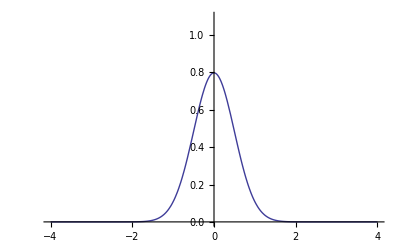
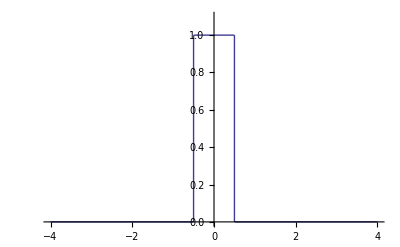
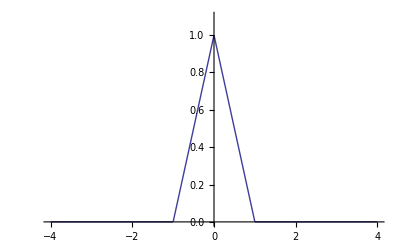

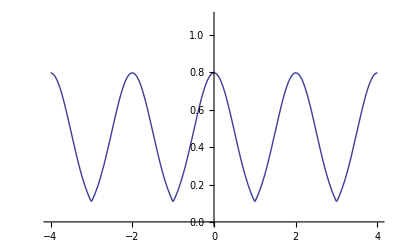
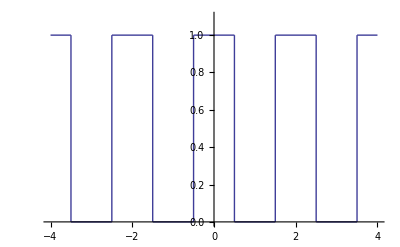
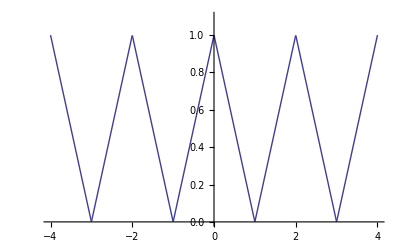

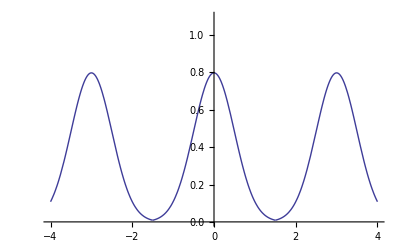
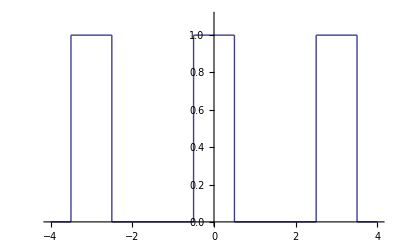

```mathematica
gauss[x_,c_,a_] := Exp[-(x-c)^2/(2 a^2)] /Sqrt[2 Pi a^2]
box[x_,c_,a_] := Piecewise[{{1,-a<(x-c)<a}},0]/(2 a)
triang[x_,c_,a_] := Piecewise[{{1+(x-c)/a,-a< (x-c)< 0},{1-(x-c)/a,0≤(x-c)< a}},0]/a

Plot[#,{x,-4,4},PlotRange->{0,1.1},ExclusionsStyle->Automatic]& /@ {gauss[x,0,1/2], box[x,0,1/2],triang[x,0,1]}

waveit[func_,period_] := func /. {x->x-period*Round[x/period]}
Plot[#,{x,-4,4},PlotRange->{0,1.1},ExclusionsStyle->Automatic]& /@ {waveit[gauss[x,0,1/2],2], waveit[box[x,0,1/2],2],waveit[triang[x,0,1],2]}
Plot[#,{x,-4,4},PlotRange->{0,1.1},ExclusionsStyle->Automatic]& /@ {waveit[gauss[x,0,1/2],3], waveit[box[x,0,1/2],3],waveit[triang[x,0,1],3]}
```

(b) Use FourierSeries to expand the function t^2 into a 4^th-order Fourier series with period τ = 2.  Include FourierParameters→{0, 2π/τ} as an option where τ is your desired period.  Then ComplexExpand the result to obtain a simpler form.  Name both the function and its series expansion.

```mathematica
func =t^2
funxexpand=FourierSeries[t^2,t,4,FourierParameters->{0,π/2}]//ComplexExpand
```

t^2

4/3-(16 Cos[(π t)/2])/π^2+(4 Cos[π t])/π^2-(16 Cos[(3 π t)/2])/(9 π^2)+Cos[2 π t]/π^2

(c) In practice, we don't actually need to force a function to be periodic.  When constructing a Fourier-series expansion of function f(t), we just assume that it is periodic and never look outside the range -τ/2 < t < +τ/2.  Plot both the function and its Fourier-series expansion from the previous cell on the same graph over the range {t, -6, 6} with PlotRange→{0,10} as an option.  Can you see how looking outside the range -τ/2 < t < +τ/2 spoils the fun?  But inside that range, the expansion works great!

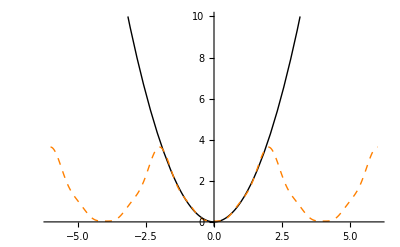

```mathematica
Plot[{func,funxexpand},{t,-6,6},PlotRange->{0,10},PlotStyle->{{Black,Thick},{Orange,Dashed}}]
```

### (#11) Numerical series expansions (10 min)

(a) Use FourierSeries to expand f(t ) = t  into 4^th-order Fourier series with period τ = 2π and ComplexExpand the result.  You won't need the FourierParameters since a period of 2π is the default.  Plot the function and it's expansion on the same graph over the range {t, -2π, 2π}.

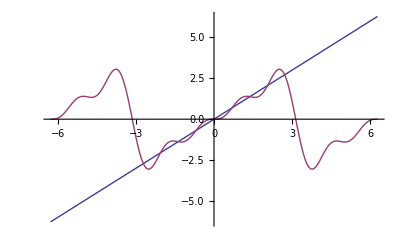

```mathematica
fst =ComplexExpand[FourierSeries[t,t,4]];
Plot[{t,fst},{t,-2π,2π}]
```

(b) Copy/paste/modify the code from the previous cell, and use NFourierSeries this time, which will obtain numeric rather than analytical coefficients.  Note that using NFourierSeries requires you to load a special package -- see the documentation.  In addition to ComplexExpand, you should process the output with Chop before plotting it to eliminate small factors that arise due to round-off error.

```mathematica
Needs["FourierSeries`"]
```

```mathematica
nfst =Chop[ComplexExpand[NFourierSeries[t,t,4]]]
Plot[{t,nfst},{t,-2π,2π}]
```

2. Sin[t]-1. Sin[2 t]+0.666667 Sin[3 t]-0.5 Sin[4 t]

-Graphics-

## Convolution (5 min)

Convolution is a integral operation on two functions, f(t) and g(t) that produces a new function:  f ∘g  = ∫_(-∞)^∞ f(τ)g(t-τ)=ⅆτ.  This operation turns out to have several desirable properties like associativity, commutativity and distributivity.  Convolution is an important operation in optics, diffraction physics, electronics, accoustics and other areas of experimental science that require one to obtain a high-resolution signal.  If we pass an audio signal, for example, through a series of components (e.g. microphone, preamplifier, A/D converter, digital filter, digital-to-analog converter, crossover network, amplifier, loudspeaker, air-filled room, ear, auditory nerve, brain), the time resolution of the final signal will depend on the limitations of each of the components along the way.  In general, we can describe the limitations of an individual component in terms of a resolution function, essentially a peak shape, where a narrow peak width indicates high resolution and a broad peak width indicates low resolution.  After convolving the resolutions functions of all of the partipating components together, the final peak has a "hybrid" shape.

### ListConvolve and ListDeconvolve (5 min)

Mathematica has some built-in functions for doing convolutions and deconvolutions with lists.  We’ll use these for a quick practical example of how they can be used to understand data.  Suppose you have a beam you want to detect which starts out as a rectangular box as in the list l1.  The box needs to be padded to have zeros in the region which overlaps the circular aperture and the beam.

It then passes through a circular aperture have a shape like the following.

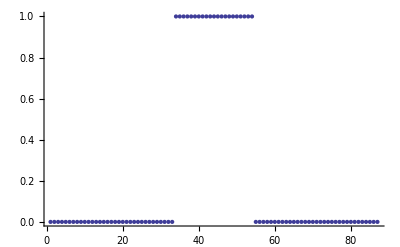

```mathematica
l1=Table[1,{x,-0.5,0.5,0.05}];
l2=Table[1.4*Sqrt[0.8^2-x^2],{x,-0.8,0.8,0.05}];
(* pad with zeroes to extend length *)
len2 = Length[l2];
l1= Join[ConstantArray[0,len2],l1,ConstantArray[0,len2]];
ListPlot[l1]
```

Here is what the circular aperture looks like.

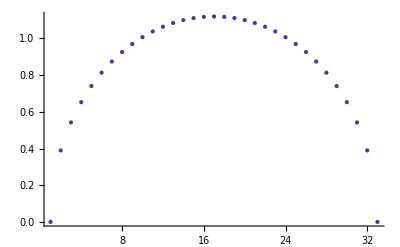

```mathematica
ListPlot[l2]
```

Finally, here the convolutionof the beam with the aperture.

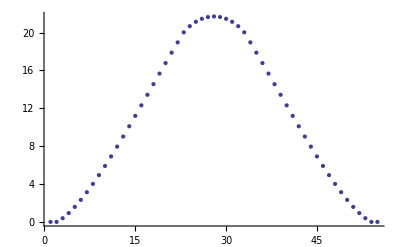

```mathematica
lc=ListConvolve[l2,l1];
ListPlot[lc]
```

You can use Deconvolute to estimate what the original beam looked like given your aperture.

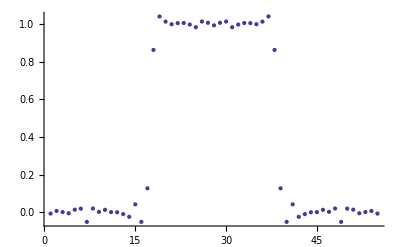

```mathematica
orig=ListDeconvolve[l2,lc];
ListPlot[orig]
```

This can be a real godsend when trying to remove instrumental smearing from many types of data.  It’s essentially like taking defocussing out of a blurred image.

### Visualization (Optional-5 min)

(a) Evaluate this cell to define several common normalized peak shapes.

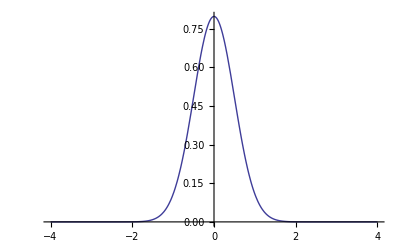
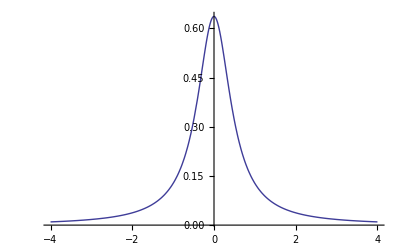
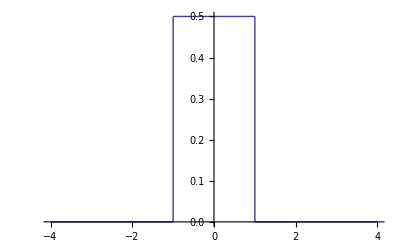
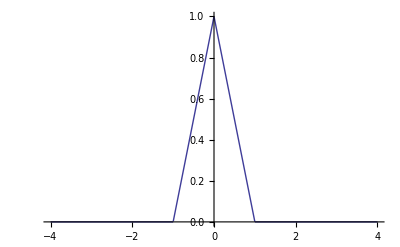

```mathematica
Clear["Global`*"]
gauss[x_,c_,a_] := Exp[-(x-c)^2/2/a^2] /Sqrt[2 Pi a^2]
lorentz[x_,c_,a_] := (a/Pi)/(x^2 + a^2)
box[x_,c_,a_] := Piecewise[{{1,-a<(x-c)<a}},0]/(2 a)
triang[x_,c_,a_] := Piecewise[{{1+(x-c)/a,-a< (x-c)< 0},{1-(x-c)/a,0≤(x-c)< a}},0]/a
Plot[#,{x,-4,4},PlotRange->All,ExclusionsStyle->Automatic]& /@ {gauss[x,0,1/2], lorentz[x,0,1/2],box[x,0,1],triang[x,0,1]}
```

(b) Evaluate this cell to create a convolution operator, and then use it to convolve two peaks together.

```mathematica
convolve[exp1_,exp2_,x_,assum_:{}] := Integrate[Evaluate[(exp1/.x->tau)(exp2/.x->x-tau)], {tau,-Infinity,Infinity},Assumptions->assum]
```

```mathematica
peak1 =box[x,0,1]
peak2 = triang[x,v,1]
peak12 = convolve[peak1,peak2,x]
```

1/2 (Piecewise[{{1, -1<x<1}, {0, True}}])

Piecewise[{{1-v+x, -1<-v+x<0}, {1+v-x, 0≤-v+x<1}, {0, True}}]

Piecewise[{{1/4, v-x==-1}, {1/4 (2-v^2+2 v x-x^2), -1<v-x<1}, {1/4 (4+4 v+v^2-4 x-2 v x+x^2), -2<v-x<-1}, {1/4 (4-4 v+v^2+4 x-2 v x+x^2), 1≤v-x<2}, {0, True}}]

(c) Evaluate this cell to visualize the convolution process.  The thick blue curve represents the convolution of the thin red curve and the thin purple curve.  The height of the convolution at any point is equal to the integrated area of overlap (the shaded area).  Demonstrate and explain this to your TA.  Also try changing the types and the widths of the peaks used -- you will need to return to the cell above.

```mathematica
seeconvolve[c_]:= Module[{p1,p2,p3,p4,p5},
p1 = Plot[peak1,{x,-3,3},ExclusionsStyle->Automatic,PlotStyle->Red,PlotRange->All];
p2 =  Plot[peak2/.v->c,{x,-3,3},ExclusionsStyle->Automatic,PlotStyle->Purple,PlotRange->All];
p3 = Plot[peak1*peak2/.v->c,{x,-3,3},ExclusionsStyle->Automatic,Filling->Axis,PlotStyle->Black,PlotRange->All];
p4 = Plot[peak12/.v->0,{x,-6,c},PlotStyle->{Thickness[0.01],Blue},PlotRange->All];
p5 = Line[{{c,0},{c,peak2/.{x->0,v->0}}}]//Graphics;
Show[{p1,p2,p3,p4,p5},PlotRange->{{-3,3},All}]
]

Manipulate[seeconvolve[c],{c,-4,4}]
```

### Width and centroid relations (Optional-5 min)

If s_1, s_2 and s_12 are the respective widths of two input peaks and their convolution, the following relation holds (exactly for Gaussians and approximately for other shapes): s_12^2 = s_1^2 + s_2^2.  This means that the convolution emphasizes the weakest link in the chain -- the final peak width will be at least as broad as the broadest component width.  

If c_1, c_2 and c_12 are the respective centroids of two input peaks and their convolution, the following relation holds:  c_12 = c_1 + c_2.

Evaluate the cell below to visualize the convolution of two Gaussians.  Demonstrate and explain the width and centroid relations to your TA.

```mathematica
peak1 = gauss[x,c1,s1]
peak2 = gauss[x,c2,s2]
peak3 = convolve[peak1,peak2,x,{x>0,s1>0,s2>0}]
```

(ⅇ^(-(-c1+x)^2/(2 s1^2)))/(√(2 π) √(s1^2))

(ⅇ^(-(-c2+x)^2/(2 s2^2)))/(√(2 π) √(s2^2))

(ⅇ^(-(c1+c2-x)^2/(2 (s1^2+s2^2))))/(√(2 π) √(s1^2+s2^2))

```mathematica
Manipulate[Plot[Evaluate[{peak1,peak2,peak3}/.{c1->cen1,c2->cen2,s1->width1,s2->width2}],{x,-20,20},PlotRange->{0,0.5},PlotStyle->{Red,Blue,{Thick,Green}}],{{cen1,-5},-10,10},{{cen2,5},-10,10},{{width1,1},0.1,5},{{width2,1},0.1,5}]
```

Plot::exclul: {Max[v - x, -1 - v + x] - 0, Max[-1 + v - x, -v + x] - 0, Min[1 + v - x, 1 - v + x] - 0} must be a list of equalities or real-valued functions.

### Motif convolution onto a comb (Optional-5 min)

Think about what would happen if you were to convolute an ordinary peak with a Dirac delta, or worse yet, a series of Dirac deltas with different amplitudes.  Evaluate the cell below to visualize the problem (purple motif convoluted with red deltas equals the blue curve).  Explain the structure of the result to your TA in terms of the width and centroid relations.

ⅇ^(-x^2)

-0.25 DiracDelta[-10+x]+0.5 DiracDelta[-5+x]-0.75 DiracDelta[5+x]+DiracDelta[10+x]

-0.25 ⅇ^(-(-10+x)^2)+0.5 ⅇ^(-(-5+x)^2)-0.75 ⅇ^(-(5+x)^2)+ⅇ^(-(10+x)^2)

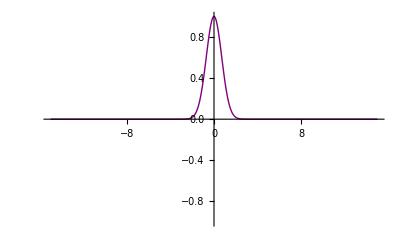
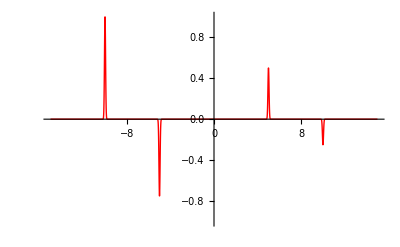
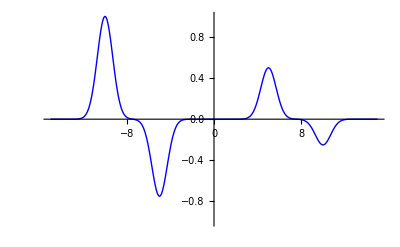

```mathematica
motif = Exp[-x^2]
comb =1 DiracDelta[x+10]-0.75*DiracDelta[x+5]+ 0.5*DiracDelta[x-5]-0.25*DiracDelta[x-10]
conv = convolve[motif,comb,x,{Im[x]==0}]

motifpic = Plot[motif,{x,-15,15},PlotStyle->{Thick,Purple},PlotRange->{-1,1}];
combpic =Plot[Evaluate[comb/. DiracDelta[x_] -> Exp[-x^2*200]],{x,-15,15},PlotStyle->{Thick,Red},PlotRange->{-1,1}];
convpic = Plot[conv,{x,-15,15},PlotStyle->{Thick,Blue},PlotRange->{-1,1}];

{motifpic ,combpic,convpic}
```

### Convolution theorem (Optional-5 min)

The convolution theorem states that the Fourier transform of the convolution of two functions is identical to the product of their individual Fourier transforms:   ℱ_[f ∘ g] =ℱ_[f ]  ℱ_[g].  This is a simple but also remarkable result.  Since Fourier transforms can often be evaulated much more quickly than integrals, use of the convolution theorem can save a lot of time on large data sets.  Evaluate the cells below to demonstrate the convolution theorem for two Gaussians with different centroids and widths.  Verify that it works.

```mathematica
f1 = gauss[x,-1,3]
f2 = gauss[x, 1,4]
```

(ⅇ^(-1/18 (1+x)^2))/(3 √(2 π))

(ⅇ^(-1/32 (-1+x)^2))/(4 √(2 π))

```mathematica
f12 = convolve[f1,f2,x,{x>0}]
FourierTransform[f12,x,k]/Sqrt[2 Pi]
```

(ⅇ^(-x^2/50))/(5 √(2 π))

(ⅇ^(-(25 k^2)/2))/(2 π)

```mathematica
F1 = FourierTransform[f1,x,k]
F2 = FourierTransform[f2,x,k]
F1*F2 //Simplify
```

ⅇ^(-1/2 k (2 ⅈ+9 k))/(√(2 π))

ⅇ^((ⅈ-8 k) k)/(√(2 π))

(ⅇ^(-(25 k^2)/2))/(2 π)

Former Physics 145 students will recognize the resolution functions described in this section as time-response functions.  Recall that the time-response function of a physical system is the FT of its frequency response function.  The fact that we can simply multiply two frequency-response curves together to get a combined frequency response is a direct consequence of the convolution theorem.  This all sounds a bit "convoluted", even if you do remember anything from Physics 145.

## Laplace transforms (optional)

### Simple transforms (15 min)

The Laplace transform (LaplaceTransform) of a function f(t) is defined as F(s) = ℒ_s[f(t)] = ∫_0^∞ f(t)ⅇ^(-s t)ⅆt.

(a) Use the integral formula above to compute ℒ_s[ⅇ^(a t)], using Assumptions→{a < s} as an option.  The result should be 1/(s-a).  Then use Mathematica's LaplaceTransform function to obtain the same result.

```mathematica
Integrate[Exp[a t]*Exp[-s t],{t,0,Infinity},Assumptions->{a<s}]
LaplaceTransform[Exp[a t],t,s]
```

1/(-a+s)

1/(-a+s)

(b) Evaluate the cell below to see that ℒ_s[t^n/(n!)] = 1/s^(n+1).   Note that FullSimplify, a more thorough extension of Simplify, knows that the Euler Gamma function can be used to compute factorials: Γ(n+1) = n!.

```mathematica
LaplaceTransform[t^n/n!,t,s]//FullSimplify
```

s^(-1-n)

(c) Compute the LaplaceTransform of each of the following functions of t :  cos(ω_0t),  cos(ω_0t) ⅇ^(a t) and J_0(ω_0 t).  Recall that BesselJ[0,x] means J_0(x).

```mathematica
LaplaceTransform[Cos[w0 t],t,s]
LaplaceTransform[Exp[a t] Cos[w0 t],t,s]
LaplaceTransform[BesselJ[0,w0 t],t,s]
```

s/(s^2+w0^2)

(-a+s)/((a-s)^2+w0^2)

1/(√(s^2+w0^2))

(d) The inverse Laplace transform (InverseLaplaceTransform) transforms F(s) back into f(t).  It's formal definition, f(t) = ℒ_t^-1[F(s)] = ∫_(γ - i ∞)^(γ + i ∞) F(s)ⅇ^(s t)ⅆt , where γ must be a real number greater than the residues of each of the singularities of F(s), is beyond the scope of our lab here -- don't worry about it.  Just compute the LaplaceTransform of sin(ω_0t) to get F(s), and then compute the InverseLaplaceTransform of F(s) in order to recover sin(ω_0t) again.

```mathematica
LaplaceTransform[Sin[w0 t],t,s]
InverseLaplaceTransform[%,s,t]
```

w0/(s^2+w0^2)

Sin[t w0]

(e) Compute the Laplace transform of the Dirac delta, δ(t), and explain the resulting F(s) to your TA.  Then inverse Laplace transform F(s) and show that you recover δ(t).

```mathematica
LaplaceTransform[DiracDelta[t],t,w]
InverseLaplaceTransform[%,w,t]
```

1

DiracDelta[t]

(f) Compute the Laplace transform of the HeavisideTheta step function.

```mathematica
LaplaceTransform[HeavisideTheta[t],t,s]
```

1/s

### Differential equations (10 min)

Laplace transforms are most commonly used to solve complicated linear systems of differential equations.  This approach is convenient because the Laplace transform of a linear differential equation is a simple polynomial equation that can often be solved by inspection.  In general, we find that ℒ_s[y^(n)(t)] = s^n ℒ_s[y(t)] - ∑_(m=0)^(n-1) s^m y^(n-1-m)(0), where y^(n)(0) represents the n^th derivative of y evaluated at time t = 0.

(a) Evaluate the cell below to obtain the Laplace transforms of several different derivatives of an undefined function y(t).  In each case we have simplified the output by renaming ℒ_s[y(t)] as Y(s).

```mathematica
LaplaceTransform[y[t],t,s]  /.  LaplaceTransform[y[t],t,s]-> Y
LaplaceTransform[y'[t],t,s]  /.  LaplaceTransform[y[t],t,s]-> Y
LaplaceTransform[y''[t],t,s]  /.  LaplaceTransform[y[t],t,s]-> Y
LaplaceTransform[y'''[t],t,s]  /.  LaplaceTransform[y[t],t,s]-> Y
LaplaceTransform[Derivative[10][y][t],t,s]  /.  LaplaceTransform[y[t],t,s]-> Y
```

Y

s Y-y[0]

s^2 Y-s y[0]-y'[0]

s^3 Y-s^2 y[0]-s y'[0]-y''[0]

s^10 Y-s^9 y[0]-s^8 y'[0]-s^7 y''[0]-s^6 y^(3)[0]-s^5 y^(4)[0]-s^4 y^(5)[0]-s^3 y^(6)[0]-s^2 y^(7)[0]-s y^(8)[0]-y^(9)[0]

(b) The time-domain differential equation for an undriven damped mechanical oscillator is  m y''[t] + b y'[t] + k y[t] == 0, where m is mass, k is the spring constant and b is the damping coefficient.  Laplace transform this equation, and then simplify the result by substituting LaplaceTransform[y[t], t, s] → Y.  Further substitute the initial position and velocity as {y[0] → 1, y'[0] → 0}.  Give the final equation a name.

```mathematica
cool = LaplaceTransform[m y''[t]+b y'[t] + k y[t]==0,t,s] /. LaplaceTransform[y[t],t,s]->Y /. {y[0] -> 1, y'[0] -> 0}
```

k Y+b (-1+s Y)+m (-s+s^2 Y)==0

(c)  Take a moment to consider how much simpler this equation is (i.e. a linear polynomial in Y).  We could do the rest of the math in our heads (though we won't).  Solve the equation for Y, and use variable replacement to obtain a simple expression in terms of s.

```mathematica
freqdep = Y/.Solve[cool,Y][[1]]
```

(b+m s)/(k+b s+m s^2)

(d)  Compute the inverse Laplace transform of Y(s) to obtain the time-dependence of the oscillator.  Then plot it over the range {t, 0, 40} for the special case where {m → 1, b → 0.3, k → 1}.

(-b ⅇ^((-b/(2 m)-(√(b^2-4 k m))/(2 m)) t)+b ⅇ^((-b/(2 m)+(√(b^2-4 k m))/(2 m)) t)+ⅇ^((-b/(2 m)-(√(b^2-4 k m))/(2 m)) t) √(b^2-4 k m)+ⅇ^((-b/(2 m)+(√(b^2-4 k m))/(2 m)) t) √(b^2-4 k m))/(2 √(b^2-4 k m))

(0.-0.252861 ⅈ) ((-0.3+1.97737 ⅈ) ⅇ^((-0.15-0.988686 ⅈ) t)+(0.3+1.97737 ⅈ) ⅇ^((-0.15+0.988686 ⅈ) t))

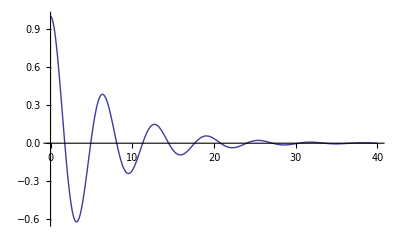

```mathematica
InverseLaplaceTransform[freqdep,s,t]
%/.{m->1,b->0.3,k->1}
Plot[%,{t,0,40},PlotRange->All]
```

## On Your Own (35 min)

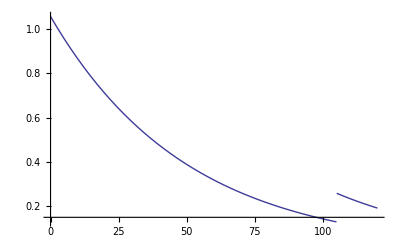

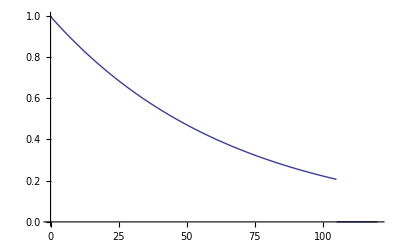

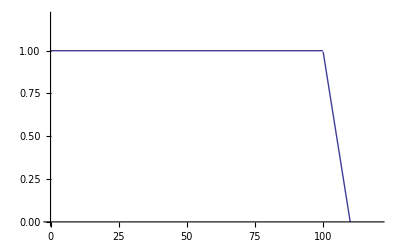

(10.-0.1 t) HeavisideTheta[-100+t]+HeavisideTheta[t]

```mathematica
Plot[HeavisideTheta[x]*(1/7Exp[-0.02*(x-100)])-HeavisideTheta[x-105]*(-1/7Exp[-0.02*(x-100)]),{x,0,120},PlotRange->All]
Plot[1/4.5(Exp[-0.015*(x-100)])-HeavisideTheta[x-105]*(1/4.5(Exp[-0.015*(x-100)])),{x,0,120},PlotRange->All]

Plot[HeavisideTheta[t]+HeavisideTheta[t-100]*(-.10*t+.1*100),{t,0,120},PlotRange->{0,1.2}]
multiply= HeavisideTheta[t]+HeavisideTheta[t-100]*(-.10*t+.1*100)
```

### (#12) Filtering Noise (15 min)

One way to reduce noise in time-series data is to filter out frequencies you don’t expect to appear in the data or you think will be a problem.  For example, line noise radiated from power lines is at 60 cycles per second and can often be suppressed.  Sometimes high frequency data is polluted by signals from nearby radio or television stations.  Another useful filter is a low-pass filter for the data.  Frequently, you expect your measurements to have no frequency components higher than a particular value.  You can reduce the noise in your data by multiplying the Fourier transform of your data by a function which is one for low frequency data and gets smaller for high frequency data.

The data file noiseyData.mat has some simulated data with high frequency noise added.  In this measurement, your detectors aren’t responsive above 100 Hz, so anything with a higher frequency than that is noise.  Use the Fourier transform take the data into the frequency domain.  Then multiplfy it by a filter function which keeps the low frequency data unaltered and reduces the high frequency data.  Then transform the data back to the frequency domain. 

Be careful in your choice of filter functions.  If you choose a sharp cut-off, it will introduce “ringing” into your data.  If you don’t know what that is, try it and you’ll see.  You may need to experiment with a few filter functions until you find one that works well for you.

```mathematica
Clear["`*"]
(*-.5 Tanh[x-100]+0.5Tanh[x-lengthOfTransform-100]+1*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

P:\My Documents\School\Semesters\Fall 2011\Physics 230\Lab Notebooks from Teacher

```mathematica
Plot[f[x],{x,0,4100}]
```

4096

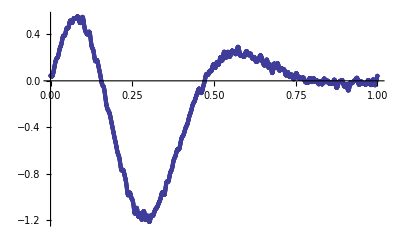

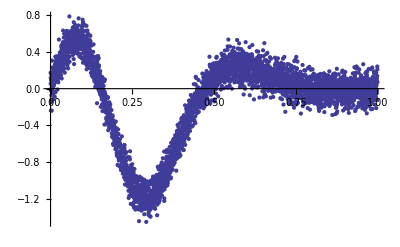

```mathematica
data =Import["noiseyData.mat"];
{time,signal} = Transpose[data[[1]]];
signal;
fourier = Fourier[signal];
l = Length[fourier]
f[x_]:= -.5 Tanh[x-100]+0.5Tanh[x-(l)+100]+1
tab = Range[1,l];
filtered = fourier*f/@tab;
toplot =Re[InverseFourier[filtered]];
plotData = Transpose[{time,toplot}];
ListPlot[plotData]
ListPlot[data]
```

### (#13) The 2D window screen (10 min)

(a) Fourier transforms can be done in more than one dimension.  In two dimensions, the Fourier Transform is  F(k) = ℱ_[f(x)] = 1/(2 π)∫_(-∞)^∞ ∫_(-∞)^∞ f(x,y)ⅇ^(i k_x x)ⅇ^(i k_y y)ⅆxⅆy.  For example, consider the following transform of a 2D box.

UnitBox[x,y]

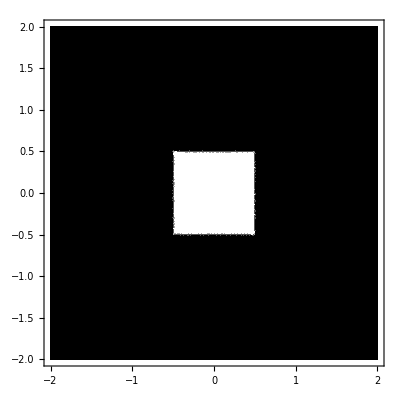

(2 Sin[kx/2] Sin[ky/2])/(kx ky π)

-Graphics3D-

```mathematica
Clear["`*"]
mask=UnitBox[x,y]
DensityPlot[mask,{x,-2,2},{y,-2,2},ColorFunction->GrayLevel, PlotPoints->100]
diffraction=FourierTransform[mask,{x,y},{kx,ky}]
Plot3D[diffraction,{kx,-20,20},{ky,-20,20},PlotRange->All,PlotPoints->75]
```

The absolute value squared on the transform is the diffraction pattern you get when light passes through a box one wavelength long on each side.

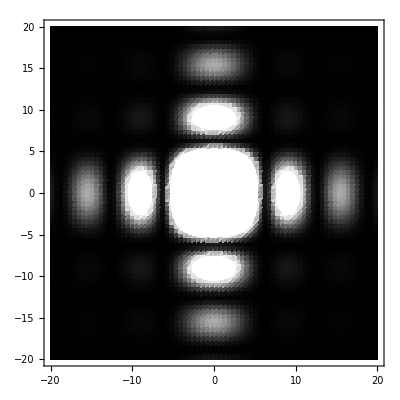

```mathematica
DensityPlot[diffraction^2,{kx,-20,20},{ky,-20,20},PlotPoints->75,ColorFunction->GrayLevel]
```

If you look through a window screen at night, you will see diffraction patterns from distant sources of light like street lamps.  You can compute this pattern in Mathematica by starting with the diffraction pattern from a single square aperture.  You’ll be looking for interference, so be sure to use the diffracted field and not the intensity (which is the absolute value squared of the field) which was plotted above.

You’ll need to generalize the box example we gave you above which is centered at the origin so that the box can have an arbitrary center.  Use Mathematica to create a function which is the diffraction pattern from a single box.  (NOTE:  Your function will be a LOT faster if you create a function from Evaluated expression for the diffracted field rather than having to do a Fourier Transform from inside your function.)

Use your function with Sum to create the field from of a 4x4 array of boxes spaced 1.2 wavelengths (λ = 2π/k) apart in the x and y directions.  This is a reasonable geometry for seeing the output of a window screen.  Create a Density Plot showing the intensity of this field using a GrayLevel ColorFunction.  You’ll probably have to adjust the number of PlotPoints and the PlotRange a bit to get a good image.

```mathematica
Clear["`*"]
```

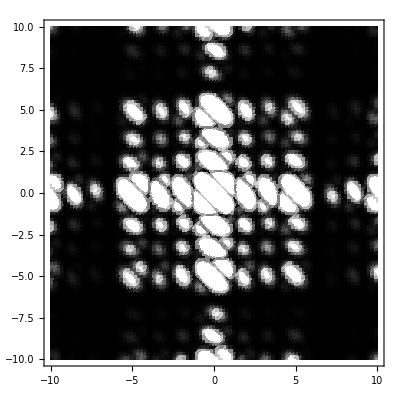

```mathematica
func[{xc_,yc_}] :=Module[{x,y},
 mymask = UnitBox[x-xc,y-yc];
Re[FourierTransform[mymask,{x,y},{kx,ky}]]//FullSimplify
];
boxes ={{0,0},{0,1.2},{0,2.4},{0,3.6},{1.2,0},{1.2,1.2},{1.2,2.4},{1.2,3.6},{2.4,0},{2.4,1.2},{2.4,2.4},{2.4,3.6},{3.6,0},{3.6,1.2},{3.6,2.4},{3.6,3.6}};
mapped = func/@boxes;
totalPic = Plus@@mapped;
DensityPlot[Abs[totalPic]^2,{kx,-10,10},{ky,-10,10},PlotPoints->100,ColorFunction->GrayLevel]
```

### (#14) Momentum Wave Function (10 min)

A particle has equal probability of being anywhere inside a sphere of radius a.  In other words ψ(x,y,z)=constant for √(x^2+y^2+z^2)<a.  In order for the probability of the particle being somewhere inside the sphere to be one, ∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞|ψ(x,y,z)|^2 ⅆzⅆyⅆx=1.  This means the constant must be equal to 1/(√V), where V is the volume of the sphere.  Since V=(4 π a^3)/3, the constant value must be √(3/(4 π a^3)).
Given the wave function ψ(x,y,z)=ψ(r,θ,ϕ)=√(3/(4 π a^3)), use a FourierTransform to find the momentum wave function ϕ[k].  Plot this probability distribution as a function of k for a sphere of radius 1.

HINT: Set up the problem in terms of a 3d Fourier transform in Cartesian coordinates, and then convert it to spherical coordinates.  Since ψ is only non-zero inside the sphere, you do the r integration from 0 to a.  The theta integration goes from 0 to π  and the ϕ integration goes from 0 to 2 π.  Recall that when you switch to spherical coordinates, dx dy dz becomes  r^2 sin(θ) dθ dϕ.  The Fourier Transform in Cartesian coordinates for three dimensions is F(k_x,k_y, k_z) = ℱ_[f(x,y,z)] = 1/(2 π)^(3/2)∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ f(x,y,z)ⅇ^(i k_x x)ⅇ^(i k_y y)ⅇ^(i k_z z)ⅆxⅆyⅆz.  Converting this to spherical coordinates, this becomes F(k,θ_k,ϕ_k)=(∫_0^∞ ∫_0^π ∫_0^(2 π) r^2 sin(θ) exp(ⅈ k.r) f(r,θ,ϕ)ⅆϕⅆθⅆr)/(2 π)^(3/2).  Since the problem is spherically symmetiric, it’s fine to take the vector k to be in any direction.  If we choose θ_k=ϕ_k=0, exp(ⅈ k.r)=exp(ⅈ k r cos(θ)).

(√(3/2) (-k Cos[k]+Sin[k]))/(k^3 π)

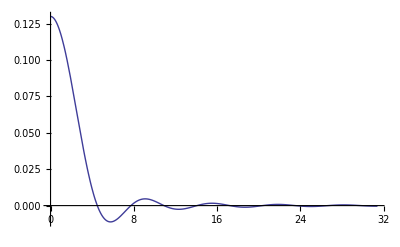

```mathematica
ψ[a_] := √(3/(4π*a^3));
plotStuff = Integrate[1/(2π)^(3/2)r^2*Sin[θ]*Exp[I*k*r*Cos[θ]]*ψ[a],{r,0,a},{θ,0,π},{ϕ,0,2π}]/.a->1
Plot[plotStuff,{k,0,10π},PlotRange->All] (*done*)
```